### Symbolic Computations

```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
xState = {x1,x2,θ1,θ2};
x2dot = (A*Sin[θ1]*Cos[θ1] + A*Sin[θ1]*θ2^2 + u) / (1 - A*Cos[θ1]^2);
θ2dot = - Sin[θ1] - (A*Sin[θ1]*Cos[θ1]^2 + A*Sin[θ1]*θ2^2*Cos[θ1] + u*Cos[θ1]) / (1 - A*Cos[θ1]^2);
diff[expr_] :=  D[expr,x1]*x2 + D[expr,x2]*x2dot + D[expr,θ1]*θ2 + D[expr,θ2]*θ2dot ;
z1 = x1 + k1*θ1 + k2*(x2*Cos[θ1] + θ2);
z2 = x2 + k1*θ2 + k2*(-Sin[θ1] - x2*Sin[θ1]*θ2)+c1*z1;
uSol = Solve[z1 + diff[z2]== -c2*z2,u];
u = (u/.uSol )[[1]];
u = Simplify[u]
```

1/(-1+k2 θ2 Sin[θ1]+Cos[θ1] (k1-k2 x2 Sin[θ1]))(x1+c1 c2 x1+c1 x2+c2 x2+k1 θ1+c1 c2 k1 θ1+c1 k1 θ2+c2 k1 θ2+k2 θ2+c1 c2 k2 θ2-A k2 (x2+c1 c2 x2-θ2-x2 θ2^2) Cos[θ1]^3-(k1+c1 k2+c2 k2+c1 k2 x2 θ2+c2 k2 x2 θ2-A θ2^2) Sin[θ1]+k2 (x2-A θ2^3) Sin[θ1]^2-A Cos[θ1]^2 (x1+c1 c2 x1+c1 x2+c2 x2+k1 θ1+c1 c2 k1 θ1+c1 k1 θ2+c2 k1 θ2+k2 θ2+c1 c2 k2 θ2-(c1+c2) k2 (1+x2 θ2) Sin[θ1])+Cos[θ1] (k2 (x2+c1 c2 x2-θ2-x2 θ2^2)+(A-A k1 θ2^2) Sin[θ1]+A k2 θ2 (-1+x2 θ2) Sin[θ1]^2))

Sanity Check

```mathematica
V = 1/2*z1^2 +1/2*z2^2;
expr = diff[V] + (c1*z1^2 + c2*z2^2);
Simplify[expr]
```

0

### Test Backstepping control on dynamics

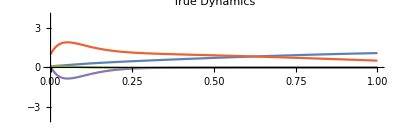

```mathematica
Tsim = 1;A = 0.2;c1 = 20;c2 = 20;k1 = 0.01;k2 = 0.01;
ICs = {0.1,0.1,0.1,1};
xNewState = {x,xdot,θ,θdot};
uff0[t_] := u/.(Table[xState[[i]]-> xNewState[[i]][t],{i,1,4}]);
eq={x'[t]==xdot[t],xdot'[t]==1/(1-A Cos[θ[t]]^2) (uff0[t]+A θdot[t]^2 Sin[θ[t]]+A Cos[θ[t]] Sin[θ[t]]),θ'[t]==θdot[t],θdot'[t]==1/(1-A Cos[θ[t]]^2) (-Sin[θ[t]]-Cos[θ[t]] (uff0[t]+A θdot[t]^2 Sin[θ[t]]))};
init={x[0]==ICs[[1]],xdot[0]==ICs[[2]],θ[0]==ICs[[3]],θdot[0]==ICs[[4]]};
{xs,xdots,θs,θdots}=NDSolveValue[{eq,init},{x,xdot,θ,θdot},{t,0,Tsim},Method->{"DiscontinuityProcessing"->None}];
Plot[{θs[t],uff0[t],xs[t],θdots[t],xdots[t]},{t,0,Tsim},Filling->{2->Axis},PlotRange->{-4,4},PlotLegends->{"θ1b","u1b","x1b","θdot1b","xdot1b"},PlotLabel->"True Dynamics ",AspectRatio->1/3,ImageSize->400,GridLines->{None,{-π,π}}]
```

Clearly the feedback is not working ( It seems to be stabilizing the system on a manifold where z1 and z2 are 0). Change Tsim to observe this
 Lets see if it is able to bring z1 and z2 to 0

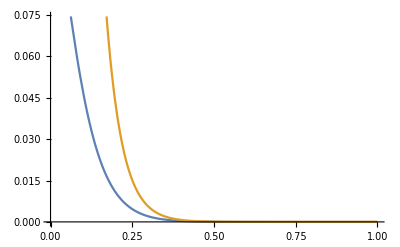

```mathematica
xSimState = {xs,xdots,θs,θdots};
z1T[t_] := z1/.(Table[xState[[i]]-> xSimState[[i]][t],{i,1,4}]);
z2T[t_] := z2/.(Table[xState[[i]]-> xSimState[[i]][t],{i,1,4}]);
Plot[{z1T[t],z2T[t]},{t,0,Tsim}]
```